```mathematica
Bo= 5*10^(-5); AUcm=1.5*10^13; A=Bo*AUcm*AUcm;Vsw=400*10^5;q=4.8032*10^(-10);mo=1.6726*10^(-24);omega=2*Pi/(27.27*86400);c=3*10^10;
```

```mathematica
GAMMA[r_,th_]:=omega*r*Sin[th]/Vsw
Br[r_,th_]:=A/(r^2)
Bth[r_,th_]:=0
Bph[r_,th_]:=-GAMMA[r,th]*A/(r^2)
BB[r_,th_]:=Br[r,th]^2 + Bth[r,th]^2 + Bph[r,th]^2
Bmod[r_,th_]:=(Br[r,th]^2 + Bth[r,th]^2 + Bph[r,th]^2)^.5
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Spherical]
```

Spherical[Rr,Ttheta,Pphi]

```mathematica
CoordinateSystem
```

Spherical

```mathematica
HeavisideTheta[1]
```

1

```mathematica
Clear[A,c,v,mo,p, omega,Vsw]
```

```mathematica
v:={Br[Rr,Ttheta],Bth[Rr,Ttheta],Bph[Rr,Ttheta]}/(BB[Rr,Ttheta])
```

```mathematica
FullSimplify[Curl[v]]
```

{-(2 omega Rr^2 Vsw^3 Cos[Ttheta])/(A (Vsw^2+omega^2 Rr^2 Sin[Ttheta]^2)^2),(2 omega Rr^2 Vsw Sin[Ttheta] (2 Vsw^2+omega^2 Rr^2 Sin[Ttheta]^2))/(A (Vsw^2+omega^2 Rr^2 Sin[Ttheta]^2)^2),(omega^2 Rr^3 Vsw^2 Sin[2 Ttheta])/(A (Vsw^2+omega^2 Rr^2 Sin[Ttheta]^2)^2)}

```mathematica
VVr[r_,th_]:=-(2*omega*r^2*Vsw^3* Cos[th])/(A *(Vsw^2+omega^2 *r^2* Sin[th]^2)^2)
VVth[r_,th_]:=(2*omega*r^2*Vsw*Sin[th]*(2*Vsw^2+omega^2*r^2*Sin[th]^2))/(A (Vsw^2+omega^2*r^2*Sin[th]^2)^2)
VVph[r_,th_]:=(omega^2*r^3*Vsw^2*Sin[2*th])/(A*(Vsw^2+omega^2*r^2*Sin[th]^2)^2)
```

```mathematica
VVr[1,2]
```

4.93225×10^-36

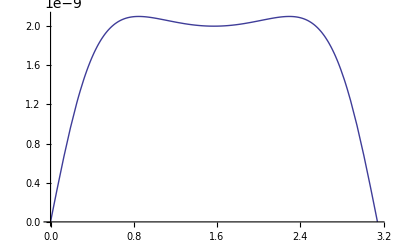

```mathematica
Plot[VVth[AUcm,th],{th,0,Pi}]
```

```mathematica
B:={Br[Rr,Ttheta],Bth[Rr,Ttheta],Bph[Rr,Ttheta]}
```

```mathematica
FullSimplify[Curl[B]]
```

{-(2 A omega Cos[Ttheta])/(Rr^2 Vsw),0,0}

```mathematica
rotBr[r_,th_]:=(-2*A*omega*Cos[th])/(r^2*Vsw)
```

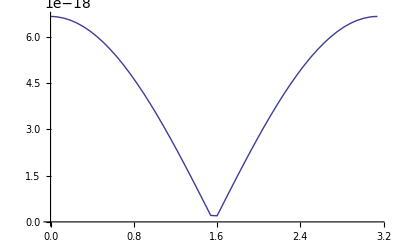

```mathematica
Plot[Abs[rotBr[1.*AUcm,th]],{th,0,Pi}]
```

```mathematica
s
```